```mathematica
strategyTag="momentum_linear";
```

```mathematica
Which[strategyTag=="maxSR"
		,SetDirectory["C:\\Users\\dongs\\Desktop\\Personal\\programming\\gitProject\\portfolioStrategy\\98_analysis_maxSR"];
		strategyTitle="maximise Sharpe Ratio(1-day)";
		strategyLabel="max. SR(1-day)";
			
	,strategyTag=="momentum_exp"
		,SetDirectory["C:\\Users\\dongs\\Desktop\\Personal\\programming\\gitProject\\portfolioStrategy\\97_analysis_momentum_exp"];
		strategyTitle="momentum(exp. weight)";
		strategyLabel="mom.(exp.)";
	,strategyTag=="momentum_linear"
		,SetDirectory["C:\\Users\\dongs\\Desktop\\Personal\\programming\\gitProject\\portfolioStrategy\\95_analysis_momentum_linear"];
		strategyTitle="momentum(lin. weight)";
		strategyLabel="mom.(lin.)";
	,strategyTag=="momentum"
		,SetDirectory["C:\\Users\\dongs\\Desktop\\Personal\\programming\\gitProject\\portfolioStrategy\\96_analysis_momentum"];
		strategyTitle="momentum";
		strategyLabel="mom.";

]
(*SetDirectory["C:\\Users\\dongs\\Desktop\\Personal\\programming\\gitProject\\portfolioStrategy"];*)
```

```mathematica
resultFiles=FileNames["*.csv"]
```

{summary_momentum_linear_no-cb_ua0_rg1_benchmark.csv,summary_momentum_linear_no-cb_ua0_rg1_portfolio.csv,summary_momentum_linear_no-cb_ua1_rg1_benchmark.csv,summary_momentum_linear_no-cb_ua1_rg1_portfolio.csv,summary_momentum_linear_no-reits_no-cb_ua0_rg1_benchmark.csv,summary_momentum_linear_no-reits_no-cb_ua0_rg1_portfolio.csv,summary_momentum_linear_no-reits_no-cb_ua1_rg1_benchmark.csv,summary_momentum_linear_no-reits_no-cb_ua1_rg1_portfolio.csv,summary_momentum_linear_no-reits_ua0_rg1_benchmark.csv,summary_momentum_linear_no-reits_ua0_rg1_portfolio.csv,summary_momentum_linear_no-reits_ua1_rg1_benchmark.csv,summary_momentum_linear_no-reits_ua1_rg1_portfolio.csv,summary_momentum_linear_ua0_rg1_benchmark.csv,summary_momentum_linear_ua0_rg1_portfolio.csv,summary_momentum_linear_ua1_rg1_benchmark.csv,summary_momentum_linear_ua1_rg1_portfolio.csv}

```mathematica
cmapLarge[x_]:=Blend[{{0.00,Purple},{0.15,Blue},{0.1875,Cyan},{0.2250,Green},{0.2575,Yellow},{0.30,Orange},{0.45,Red},{1.0,White}},x/100];
```

```mathematica
getDates[day_]:=Which[day≥0&&day<5,Log[4,1+3*day](*day*)
					,day≥5&&day<20,1/15*(day-5)+2(* week*)
					,day≥20&&day<40,1/20*(day-20)+3(*month*)
					,day≥40&&day<60,1/20*(day-40)+4(*2-month*)
					,day≥60&&day<120,1/60*(day-60)+5(*3-month*)
					,day≥120&&day<225,1/105*(day-120)+6(*6-month, half year*)
					,day≥225,1/225*(day-225)+7(*year*)
				];
```

```mathematica
transformData[data_]:=Module[{$i,$result},
							$result=data;
							For[$i=1,$i≤Length[data],$i++,
									$result[[$i,1]]=getDates[$result[[$i,1]]];
									$result[[$i,2]]=getDates[$result[[$i,2]]];
								];
							$result
							];
```

```mathematica
lticks={{1,Style["day",Black,50,FontFamily->"Times"],{0.03,0}}
		,{2,Style["week",Black,50,FontFamily->"Times"],{0.03,0}}
		,{3,Style["mo.",Black,50,FontFamily->"Times"],{0.03,0}}
		,{4,Style["2 mos.",Black,50,FontFamily->"Times"],{0.03,0}}
		,{5,Style["3 mos.",Black,50,FontFamily->"Times"],{0.03,0}}
		,{6,Style["6 mos.",Black,50,FontFamily->"Times"],{0.03,0}}
		,{7,Style["year",Black,50,FontFamily->"Times"],{0.03,0}}
		};
bticks=ticksWoL=Transpose[{Transpose[lticks][[1]],Table[Rotate[Transpose[lticks][[2]][[i]],45],{i,1,Length[Transpose[lticks][[2]]]}], Transpose[lticks][[3]]}];
ticksWoL=Transpose[{Transpose[lticks][[1]],Table["",{i,1,Length[Transpose[lticks][[2]]]}], Transpose[lticks][[3]]}];
barTicks=Table[If[Mod[i,20]==0
				,{i,Style[ToString[i]<>"%",40,Black,FontFamily->"Times"],{0.07,0.07}}
				,If[Mod[i,10]==0
					,{i,"",{0.06,0.06}}
					,{i,"",{0.05,0.05}}
					]
				]
			,{i,0,100,2}];
```

```mathematica
drawLarge[tag_?StringQ,icol_?IntegerQ,strategy_?StringQ,variable_?StringQ,stock_?StringQ,bond_?StringQ,gold_?StringQ,reits_?StringQ,cb_?StringQ,srGuage_?IntegerQ]:=
	Module[{pDat,bDat,pFig,bFig,barlegend},
		pDat= transformData[Import["summary_"<>strategyTag<>"_"<>tag<>"_portfolio.csv","CSV"][[2;;,{1,2,icol}]]];
		bDat= transformData[Import["summary_"<>strategyTag<>"_"<>tag<>"_benchmark.csv","CSV"][[2;;,{1,2,icol}]]];
		pFig=ListContourPlot[pDat[[;;,{1,2,3}]]
							,PlotLabel->Style["Portfolio",Black,60,FontFamily->"Times"]
							,FrameStyle->{Directive[Black,Thickness[0.005],30,FontFamily->"Times"]
										,Directive[Black,Thickness[0.005],30,FontFamily->"Times"]
										}
							,FrameLabel->{Style["Reblancing period",60,FontFamily->"Times",Black]
										,Style["Lookback period",60,FontFamily->"Times",Black]
										}
							,FrameTicksStyle->Directive[50,FontFamily->"Times"]
							,FrameTicks->{{lticks,ticksWoL},{bticks,ticksWoL}}
							,AspectRatio->1/1.125
							,ImageSize-> {700+210,240+700/1.125}
							,ImageMargins->{{0,-10},{0,0}}
							,ImagePadding->{{200,10},{220,20}}
							,InterpolationOrder->5
							,Contours-> Range[0,100,0.5]
							,ContourLabels->True
							,ColorFunctionScaling->False
							,ColorFunction->cmapLarge
							,Epilog->{Text[Style[strategy ,40,FontFamily->"Times",Black],{4,3.5},{-1,0}]
									,Text[Style[variable ,40,FontFamily->"Times",Black],{4,3},{-1,0}]									
									}
			];
		bFig=ListContourPlot[bDat[[;;,{1,2,3}]]
							,PlotLabel->Style["Benchmark",Black,60,FontFamily->"Times"]
							,FrameStyle->{Directive[Black,Thickness[0.005],30,FontFamily->"Times"]
										,Directive[Black,Thickness[0.005],30,FontFamily->"Times"]
										}
							,FrameLabel->{Style["Rebalancing period",60,FontFamily->"Times",Black]
										,Style["",60,FontFamily->"Times",Black]
										}
							,FrameTicksStyle->Directive[50,FontFamily->"Times"]
							,FrameTicks->{{ticksWoL,ticksWoL},{bticks,ticksWoL}}
							,AspectRatio->1/1.125
							,ImageSize-> {20+700,240+700/1.125}
							,ImageMargins->{{-10,0},{0,0}}
							,ImagePadding->{{10,10},{220,20}}
							,InterpolationOrder->5
							,Contours-> Range[0,100,0.1]
							,ContourLabels->All
							,ColorFunctionScaling->False
							,ColorFunction->cmapLarge
							(*,PlotLegends->Placed[BarLegend[{cmapMDD[#]&,{0,100}}
														,FrameStyle-> Directive[Black,Thickness[0.005]]
														,Ticks->barTicks
														,LegendMarkerSize->{50,1000/1.125-200}
														,LegendMargins->{{0,0},{180,00}}(*{{0,0},{220,25}}*)
												]
												,{1,0.5}
											]*)
							,Epilog->{Text[Style["Stock : "<>stock ,40,FontFamily->"Times",Black],{4.5,4.1},{-1,0}]
									,Text[Style["Bond  : "<>bond ,40,FontFamily->"Times",Black],{4.5,3.7},{-1,0}]
									,Text[Style["Gold  : "<>gold ,40,FontFamily->"Times",Black],{4.5,3.3},{-1,0}]
									,Text[Style["REITs : "<>reits ,40,FontFamily->"Times",Black],{4.5,2.9},{-1,0}]
									,Text[Style["C.B.  : "<>cb ,40,FontFamily->"Times",Black],{4.5,2.5},{-1,0}]								
									}
			];
			(*barlegend=BarLegend[{cmapMDD[#]&,{0,100}}
								,FrameStyle-> Directive[Black,Thickness[0.005]]
								,Ticks->barTicks
								,LegendMarkerSize->{50,1000/1.125-200}
								,LegendMargins->{{0,0},{0,0}}(*{{0,0},{220,25}}*)
					];*)
			barlegend=ContourPlot[y,{x,0,1},{y,0,100}
								,PlotRange->{{0,1},{0,100}}
								,ColorFunctionScaling->False
								,ColorFunction->cmapLarge
								,Contours->200
								,ContourLines->False
								,FrameStyle->{Directive[Black,Thickness[0.035],30,FontFamily->"Times"]
											,Directive[Black,Thickness[0.035],30,FontFamily->"Times"]
											}
								,FrameTicks->{{None,barTicks},{None,None}}
								,ImageSize-> {700/(1.125*15)+100,260+700/1.125}
								,ImagePadding->{{0,100},{220,40}}
								,AspectRatio->15
					];
			(*Print[pDat];*)
			(*Print[bDat];*)
			Grid[{{Show[pFig],Show[bFig],Show[barlegend]}}
				,Alignment->Center 
				,Spacings->{0,0}]
			
	];
```

```mathematica
points={0.95,0.96,0.97,0.98,0.99,1.0,1.01,1.02,1.03,1.04,1.05,1.07,1.1,1.15,1.2,1.3,1.4,1.5,1.6};
cmapColors=Table[ColorData["Pastel"][i/Length[points]],{i,1,Length[points]}];

cmapSmall[x_]:=Blend[Table[{(Log[points[[i]]]-Log[points[[1]]])/(Log[points[[-1]]]-Log[points[[1]]]),cmapColors[[i]]},{i,1,Length[points]}],(Log[1+0.01x]-Log[points[[1]]])/(Log[points[[-1]]]-Log[points[[1]]])];
```

```mathematica
barTicksSmall={{-5,Style["-5%",Black,40,FontFamily->"Times"],{0.07,0.07}}
		(*,{-3,Style["-3%",Black,40,FontFamily->"Times"],{0.07,0.07}}
		,{-1,Style["-1%",Black,40,FontFamily->"Times"],{0.07,0.07}}*)
		,{0,Style["0%",Black,40,FontFamily->"Times"],{0.07,0.07}}
		(*,{1,Style["1%",Black,40,FontFamily->"Times"],{0.07,0.07}}
		,{3,Style["3%",Black,40,FontFamily->"Times"],{0.07,0.07}}*)
		,{5,Style["5%",Black,40,FontFamily->"Times"],{0.07,0.07}}
		,{10,Style["10%",Black,40,FontFamily->"Times"],{0.07,0.07}}
		,{20,Style["20%",Black,40,FontFamily->"Times"],{0.07,0.07}}
		,{30,Style["30%",Black,40,FontFamily->"Times"],{0.07,0.07}}
		,{40,Style["40%",Black,40,FontFamily->"Times"],{0.07,0.07}}
		};
For[i=-4,i≤40,i++,
	If[Not[MemberQ[Transpose[barTicksSmall][[1]],i]]
			,AppendTo[barTicksSmall,{i,"",{0.05,0.05}}]
			,Nothing
	]
]
```

```mathematica
drawSmall[tag_?StringQ,icol_?IntegerQ,strategy_?StringQ,variable_?StringQ,stock_?StringQ,bond_?StringQ,gold_?StringQ,reits_?StringQ,cb_?StringQ,srGuage_?IntegerQ]:=
	Module[{pDat,bDat,pFig,bFig,barlegendSmall},
		pDat= transformData[Import["summary_"<>strategyTag<>"_"<>tag<>"_portfolio.csv","CSV"][[2;;,{1,2,icol}]]];
		bDat= transformData[Import["summary_"<>strategyTag<>"_"<>tag<>"_benchmark.csv","CSV"][[2;;,{1,2,icol}]]];
		pFig=ListContourPlot[pDat[[;;,{1,2,3}]]
							,PlotLabel->Style["Portfolio",Black,60,FontFamily->"Times"]
							,FrameStyle->{Directive[Black,Thickness[0.005],30,FontFamily->"Times"]
										,Directive[Black,Thickness[0.005],30,FontFamily->"Times"]
										}
							,FrameLabel->{Style["Reblancing period",60,FontFamily->"Times",Black]
										,Style["Lookback period",60,FontFamily->"Times",Black]
										}
							,FrameTicksStyle->Directive[50,FontFamily->"Times"]
							,FrameTicks->{{lticks,ticksWoL},{bticks,ticksWoL}}
							,AspectRatio->1/1.125
							,ImageSize-> {700+210,240+700/1.125}
							,ImageMargins->{{0,-10},{0,0}}
							,ImagePadding->{{200,10},{220,20}}
							,InterpolationOrder->5
							,Contours-> 30
							,ContourLabels->True
							,ColorFunctionScaling->False
							,ColorFunction->cmapSmall
							,Epilog->{Text[Style[strategy ,40,FontFamily->"Times",Black],{4,3.5},{-1,0}]
									,Text[Style[variable ,40,FontFamily->"Times",Black],{4,3},{-1,0}]									
									}
			];
		bFig=ListContourPlot[bDat[[;;,{1,2,3}]]
							,PlotLabel->Style["Benchmark",Black,60,FontFamily->"Times"]
							,FrameStyle->{Directive[Black,Thickness[0.005],30,FontFamily->"Times"]
										,Directive[Black,Thickness[0.005],30,FontFamily->"Times"]
										}
							,FrameLabel->{Style["Rebalancing period",60,FontFamily->"Times",Black]
										,Style["",60,FontFamily->"Times",Black]
										}
							,FrameTicksStyle->Directive[50,FontFamily->"Times"]
							,FrameTicks->{{ticksWoL,ticksWoL},{bticks,ticksWoL}}
							,AspectRatio->1/1.125
							,ImageSize-> {20+700,240+700/1.125}
							,ImageMargins->{{-10,0},{0,0}}
							,ImagePadding->{{10,10},{220,20}}
							,InterpolationOrder->5
							,Contours-> 30
							,ContourLabels->All
							,ColorFunctionScaling->False
							,ColorFunction->cmapSmall
							,Epilog->{Text[Style["Stock : "<>stock ,40,FontFamily->"Times",Black],{4.5,4.1},{-1,0}]
									,Text[Style["Bond  : "<>bond ,40,FontFamily->"Times",Black],{4.5,3.7},{-1,0}]
									,Text[Style["Gold  : "<>gold ,40,FontFamily->"Times",Black],{4.5,3.3},{-1,0}]
									,Text[Style["REITs : "<>reits ,40,FontFamily->"Times",Black],{4.5,2.9},{-1,0}]
									,Text[Style["C.B.  : "<>cb ,40,FontFamily->"Times",Black],{4.5,2.5},{-1,0}]								
									}
			];
			barlegendSmall=ContourPlot[y,{x,0,1},{y,-5,40}
									,PlotRange->{{0,1},{-5,40}}
									,ColorFunctionScaling->False
									,ColorFunction->cmapSmall
									,Contours->200
									,ContourLines->False
									,FrameStyle->{Directive[Black,Thickness[0.035],30,FontFamily->"Times"]
											,Directive[Black,Thickness[0.035],30,FontFamily->"Times"]
											}
									,FrameTicks->{{None,barTicksSmall},{None,None}}
									,ImageSize-> {700/(1.125*15)+100,260+700/1.125}
									,ImagePadding->{{0,100},{220,40}}
									,AspectRatio->15
							];
			(*Print[pDat];
			Print[bDat];*)
			Grid[{{Show[pFig],Show[bFig],Show[barlegendSmall]}}
				,Alignment->Center 
				,Spacings->{0,0}]
			
	];
```

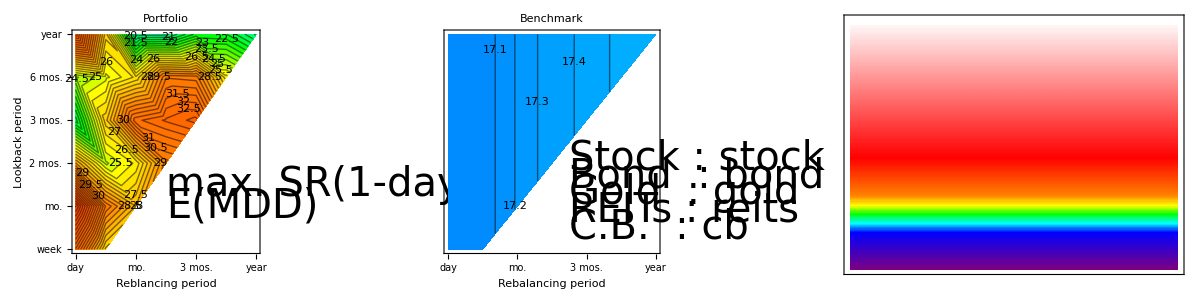

```mathematica
(*Export["test_out.pdf",drawMDD["no-reits_no-cb_ua0_rg1","none","none",1]];*)
drawLarge["no-reits_no-cb_ua0_rg1",3,"max. SR(1-day)","E(MDD)","stock","bond","gold","reits","cb",1]
```

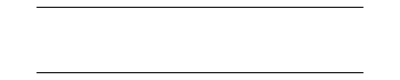
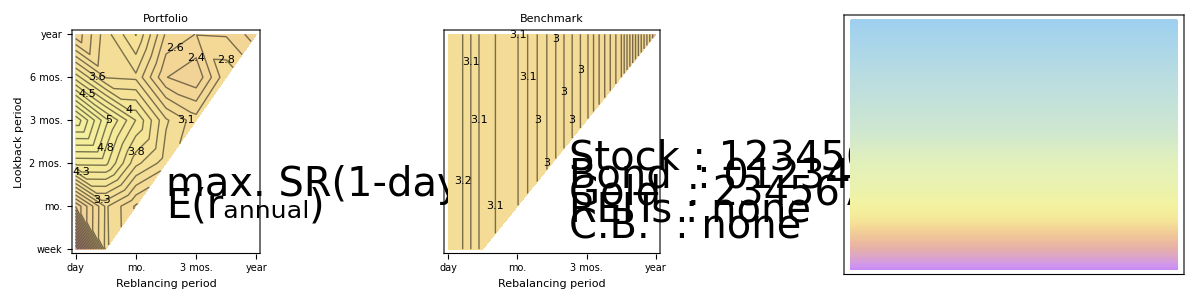
Hi
-Graphics-
-Graphics-

```mathematica
(*drawSmall["no-reits_no-cb_ua0_rg1","none","none",1]*)
Grid[{{Text[Style["Hi",Black,70,FontFamily->"Times"]]}
,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.002]]
		,Style[Line[{{-1,-0.05},{1,-0.05}}],Thickness[0.002]]}
	,ImageSize->Automatic->{1200,20},AspectRatio->Automatic]
	}
,{drawSmall["no-reits_no-cb_ua0_rg1",7,"max. SR(1-day)","E(r_annual)","123456","012345","234567","none","none",1]}
}]
```

```mathematica
assetTags={"","no-cb_","no-reits_","no-reits_no-cb_"};
cbs={"239660","none","239660","none"};
reits={"182480","182480","none","none"};
```

```mathematica
For[i1=1,i1≤Length[assetTags],i1++,
	(*ua = 0*)
	fig$ua0$mdd=Grid[{{Text[Style[strategyTitle,Black,70,FontFamily->"Times"]]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.002]]
				,Style[Line[{{-1,-0.05},{1,-0.05}}],Thickness[0.002]]}
				,ImageSize->Automatic->{1200,20},AspectRatio->Automatic]
				}
				(*E(MDD)*)
				,{Text[Style["E(MDD)",Black,50,FontFamily->"Times"]]}
				,{drawLarge[assetTags[[i1]]<>"ua0_rg1",3,strategyLabel,"E(MDD)","069500","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*σ(MDD)*)
				,{Text[Style["σ(MDD)",Black,50,FontFamily->"Times"]]}
				,{drawLarge[assetTags[[i1]]<>"ua0_rg1",4,strategyLabel,"σ(MDD)","069500","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*min(MDD)*)
				,{Text[Style["min(MDD)",Black,50,FontFamily->"Times"]]}
				,{drawLarge[assetTags[[i1]]<>"ua0_rg1",5,strategyLabel,"min(MDD)","069500","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*max(MDD)*)
				,{Text[Style["max(MDD)",Black,50,FontFamily->"Times"]]}
				,{drawLarge[assetTags[[i1]]<>"ua0_rg1",6,strategyLabel,"max(MDD)","069500","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				}];
	fig$ua0$ar=Grid[{{Text[Style[strategyTitle,Black,70,FontFamily->"Times"]]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.002]]
				,Style[Line[{{-1,-0.05},{1,-0.05}}],Thickness[0.002]]}
				,ImageSize->Automatic->{1200,20},AspectRatio->Automatic]
				}
				(*E(ar)*)
				,{Text[Style["E(r_annual)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua0_rg1",7,strategyLabel,"E(r_annual)","069500","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*σ(MDD)*)
				,{Text[Style["σ(r_annual)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua0_rg1",8,strategyLabel,"σ(r_annual)","069500","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*min(MDD)*)
				,{Text[Style["min(r_annual)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua0_rg1",9,strategyLabel,"min(r_annual)","069500","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*max(MDD)*)
				,{Text[Style["max(r_annual)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua0_rg1",10,strategyLabel,"max(r_annual)","069500","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				}];
	fig$ua0$sr1=Grid[{{Text[Style[strategyTitle,Black,70,FontFamily->"Times"]]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.002]]
				,Style[Line[{{-1,-0.05},{1,-0.05}}],Thickness[0.002]]}
				,ImageSize->Automatic->{1200,20},AspectRatio->Automatic]
				}
				(*E(ar)*)
				,{Text[Style["E(SR_1) ( SR_1 : daily Sharpe ratio)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua0_rg1",11,strategyLabel,"E(SR_1)","069500","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*σ(MDD)*)
				,{Text[Style["σ(SR_1)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua0_rg1",12,strategyLabel,"σ(SR_1)","069500","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*min(MDD)*)
				,{Text[Style["min(SR_1)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua0_rg1",13,strategyLabel,"min(SR_1)","069500","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*max(MDD)*)
				,{Text[Style["max(SR_1)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua0_rg1",14,strategyLabel,"max(SR_1)","069500","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				}];
	Export["./ua0_rg1_"<>assetTags[[i1]]<>"MDD.pdf",fig$ua0$mdd];
	Export["./ua0_rg1_"<>assetTags[[i1]]<>"AnnualReturn.pdf",fig$ua0$ar];
	Export["./ua0_rg1_"<>assetTags[[i1]]<>"SR_1-day.pdf",fig$ua0$sr1];
	(*ua = 1*)
	(*Export["./test_"<>assetTags[[i1]]<>"ua1.pdf",drawLarge[assetTags[[i1]]<>"ua1_rg1",3,strategyLabel,"E(r_annual)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]];*)
	fig$ua1$mdd=Grid[{{Text[Style[strategyTitle,Black,70,FontFamily->"Times"]]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.002]]
				,Style[Line[{{-1,-0.05},{1,-0.05}}],Thickness[0.002]]}
				,ImageSize->Automatic->{1200,20},AspectRatio->Automatic]
				}
				(*E(MDD)*)
				,{Text[Style["E(MDD)",Black,50,FontFamily->"Times"]]}
				,{drawLarge[assetTags[[i1]]<>"ua1_rg1",3,strategyLabel,"E(MDD)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*σ(MDD)*)
				,{Text[Style["σ(MDD)",Black,50,FontFamily->"Times"]]}
				,{drawLarge[assetTags[[i1]]<>"ua1_rg1",4,strategyLabel,"σ(MDD)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*min(MDD)*)
				,{Text[Style["min(MDD)",Black,50,FontFamily->"Times"]]}
				,{drawLarge[assetTags[[i1]]<>"ua1_rg1",5,strategyLabel,"min(MDD)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*max(MDD)*)
				,{Text[Style["max(MDD)",Black,50,FontFamily->"Times"]]}
				,{drawLarge[assetTags[[i1]]<>"ua1_rg1",6,strategyLabel,"max(MDD)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				}];
	fig$ua1$ar=Grid[{{Text[Style[strategyTitle,Black,70,FontFamily->"Times"]]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.002]]
				,Style[Line[{{-1,-0.05},{1,-0.05}}],Thickness[0.002]]}
				,ImageSize->Automatic->{1200,20},AspectRatio->Automatic]
				}
				(*E(ar)*)
				,{Text[Style["E(r_annual)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua1_rg1",7,strategyLabel,"E(r_annual)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*σ(MDD)*)
				,{Text[Style["σ(r_annual)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua1_rg1",8,strategyLabel,"σ(r_annual)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*min(MDD)*)
				,{Text[Style["min(r_annual)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua1_rg1",9,strategyLabel,"min(r_annual)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*max(MDD)*)
				,{Text[Style["max(r_annual)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua1_rg1",10,strategyLabel,"max(r_annual)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				}];
	fig$ua1$sr1=Grid[{{Text[Style[strategyTitle,Black,70,FontFamily->"Times"]]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.002]]
				,Style[Line[{{-1,-0.05},{1,-0.05}}],Thickness[0.002]]}
				,ImageSize->Automatic->{1200,20},AspectRatio->Automatic]
				}
				(*E(ar)*)
				,{Text[Style["E(SR_1) ( SR_1 : daily Sharpe ratio)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua1_rg1",11,strategyLabel,"E(SR_1)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*σ(MDD)*)
				,{Text[Style["σ(SR_1)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua1_rg1",12,strategyLabel,"σ(SR_1)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*min(MDD)*)
				,{Text[Style["min(SR_1)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua1_rg1",13,strategyLabel,"min(SR_1)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				(*max(MDD)*)
				,{Text[Style["max(SR_1)",Black,50,FontFamily->"Times"]]}
				,{drawSmall[assetTags[[i1]]<>"ua1_rg1",14,strategyLabel,"max(SR_1)","069660","114100","132030",reits[[i1]],cbs[[i1]],1]}
				,{Graphics[{Style[Line[{{-1,0},{1,0}}],Thickness[0.0007],Dashing[{0.01,0.01}]]},ImageSize->Automatic->{1200,20},AspectRatio->Automatic]}
				}];
	Export["./ua1_rg1_"<>assetTags[[i1]]<>"MDD.pdf",fig$ua1$mdd];
	Export["./ua1_rg1_"<>assetTags[[i1]]<>"AnnualReturn.pdf",fig$ua1$ar];
	Export["./ua1_rg1_"<>assetTags[[i1]]<>"SR_1-day.pdf",fig$ua1$sr1];
	Clear[fig$ua0$mdd,fig$ua0$ar,fig$ua0$sr1,fig$ua1$mdd,fig$ua1$ar,fig$ua1$sr1];
]
```